```mathematica
(*Mathematica*)
```

```mathematica
{Z0,Z1,Z2,Z3}={1,0,x+I*y,z+t}
```

{1,0,x+ⅈ y,t+z}

```mathematica
m=(i/Sqrt[2])*{{z+y,x+I*y},{x-I*y,-z+t}}
```

{{(i (y+z))/(√2),(i (x+ⅈ y))/(√2)},{(i (x-ⅈ y))/(√2),(i (t-z))/(√2)}}

```mathematica
w=ExpandAll[{Z0,Z1}-m.{Z2,Z3}]
```

{1-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)-(ⅈ i y^2)/(√2)-√2 i x z-ⅈ √2 i y z,-(i t^2)/(√2)-(i x^2)/(√2)-(i y^2)/(√2)+(i z^2)/(√2)}

```mathematica
{Z0b,Z1b,Z2b,Z3b}={0,1,x-I*y,-z+t}
```

{0,1,x-ⅈ y,t-z}

```mathematica
v=ExpandAll[{Z0b,Z1b}-m.{Z2b,Z3b}]
```

{-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)+(ⅈ i y^2)/(√2)+ⅈ √2 i y z,1-(i t^2)/(√2)-(i x^2)/(√2)+ⅈ √2 i x y+(i y^2)/(√2)+√2 i t z-(i z^2)/(√2)}

```mathematica
u=Join[w,v]
```

{1-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)-(ⅈ i y^2)/(√2)-√2 i x z-ⅈ √2 i y z,-(i t^2)/(√2)-(i x^2)/(√2)-(i y^2)/(√2)+(i z^2)/(√2),-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)+(ⅈ i y^2)/(√2)+ⅈ √2 i y z,1-(i t^2)/(√2)-(i x^2)/(√2)+ⅈ √2 i x y+(i y^2)/(√2)+√2 i t z-(i z^2)/(√2)}

```mathematica
Solve[Table[u[[i]]==0,{i,4}],{x,y,z,t}]
```

{{x→(-306937805/35218947624078299187-(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(242980452096+132941027056 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(1203526246400+153658294272 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2)),y→-√(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214),z→(-306937805/281751580992626393496-(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(1112274465312+1430756913272 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2)),t→(-1534689025/93917193664208797832-(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(69002605472+82092336120 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(1027869806592+114320539648 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2))},{x→(306937805/35218947624078299187+(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(242980452096+132941027056 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(1203526246400+153658294272 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2)),y→√(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214),z→(306937805/281751580992626393496+(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(1112274465312+1430756913272 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2)),t→(1534689025/93917193664208797832+(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)-(69002605472+82092336120 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(3/2)+(1027869806592+114320539648 ⅈ) (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root-0.474+0.0173 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,1}]-0.4737758355568214)^(7/2))},{x→(-306937805/35218947624078299187-(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(242980452096+132941027056 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(1203526246400+153658294272 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2)),y→-√(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204),z→(-306937805/281751580992626393496-(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(1112274465312+1430756913272 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2)),t→(-1534689025/93917193664208797832-(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(69002605472+82092336120 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(1027869806592+114320539648 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2))},{x→(306937805/35218947624078299187+(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(242980452096+132941027056 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(1203526246400+153658294272 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2)),y→√(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204),z→(306937805/281751580992626393496+(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(1112274465312+1430756913272 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2)),t→(1534689025/93917193664208797832+(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)-(69002605472+82092336120 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(3/2)+(1027869806592+114320539648 ⅈ) (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root-0.0347+8.67 × 10^-3 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,2}]-0.03470457081395204)^(7/2))},{x→(-306937805/35218947624078299187-(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(242980452096+132941027056 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(1203526246400+153658294272 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2)),y→-√(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137),z→(-306937805/281751580992626393496-(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(1112274465312+1430756913272 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2)),t→(-1534689025/93917193664208797832-(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(69002605472+82092336120 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(1027869806592+114320539648 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2))},{x→(306937805/35218947624078299187+(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(242980452096+132941027056 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(1203526246400+153658294272 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2)),y→√(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137),z→(306937805/281751580992626393496+(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(1112274465312+1430756913272 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2)),t→(1534689025/93917193664208797832+(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)-(69002605472+82092336120 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(3/2)+(1027869806592+114320539648 ⅈ) (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root0.0847+0.234 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,3}]0.08472414572794137)^(7/2))},{x→(-306937805/35218947624078299187-(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(242980452096+132941027056 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(1203526246400+153658294272 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2)),y→-√(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921),z→(-306937805/281751580992626393496-(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(1112274465312+1430756913272 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2)),t→(-1534689025/93917193664208797832-(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(69002605472+82092336120 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(1027869806592+114320539648 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2))},{x→(306937805/35218947624078299187+(1021131116 ⅈ)/58698246040130498645) ((131117928940+96757348819 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(242980452096+132941027056 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(1203526246400+153658294272 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(3522869198848+1690385252352 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2)),y→√(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921),z→(306937805/281751580992626393496+(255282779 ⅈ)/117396492080260997290) ((1088893705580+897584945873 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(1112274465312+1430756913272 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(24356843130880+3543463624704 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(46408198455296+17920761790464 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2)),t→(1534689025/93917193664208797832+(765848337 ⅈ)/23479298416052199458) ((25078734892+34701363169 ⅈ) √(Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)-(69002605472+82092336120 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(3/2)+(1027869806592+114320539648 ⅈ) (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(5/2)+(1809324113920+702209589248 ⅈ) √2 (Root0.109-0.171 ⅈRoot[{-2+#1^2&,1+#2^2&,1800+32097 #1 #3+8240 #1 #2 #3-69616 #3^2-47744 #2 #3^2+475136 #1 #3^3-102400 #1 #2 #3^3+2097152 #3^4+131072 #2 #3^4&},{2,2,4}]0.10889426736642921)^(7/2))}}

```mathematica
s={x,y,z,t}/.NSolve[Table[u[[i]]==0,{i,4}],{x,y,z,t}]
```

{{-0.257071+0.487324 ⅈ,0.394874-0.216867 ⅈ,-0.0267151-0.423278 ⅈ,-0.414349-0.536312 ⅈ},{0.257071-0.487324 ⅈ,-0.394874+0.216867 ⅈ,0.0267151+0.423278 ⅈ,0.414349+0.536312 ⅈ},{-0.235789-0.37755 ⅈ,-0.408415-0.286493 ⅈ,0.271735+0.711244 ⅈ,-0.0194558+0.655884 ⅈ},{0.235789+0.37755 ⅈ,0.408415+0.286493 ⅈ,-0.271735-0.711244 ⅈ,0.0194558-0.655884 ⅈ},{-0.161709+0.0932893 ⅈ,0.0125752+0.688429 ⅈ,-0.444503-0.342151 ⅈ,-0.761679-0.208114 ⅈ},{0.161709-0.0932893 ⅈ,-0.0125752-0.688429 ⅈ,0.444503+0.342151 ⅈ,0.761679+0.208114 ⅈ},{0.650447+0.00860786 ⅈ,-0.0230976-0.187718 ⅈ,0.695546+0.0593131 ⅈ,0.318775+0.0982518 ⅈ},{-0.650447-0.00860786 ⅈ,0.0230976+0.187718 ⅈ,-0.695546-0.0593131 ⅈ,-0.318775-0.0982518 ⅈ}}

```mathematica
Length[s]
```

8

```mathematica
Abs[s]
```

{{0.550972,0.450507,0.42412,0.677728},{0.550972,0.450507,0.42412,0.677728},{0.445129,0.49888,0.761385,0.656172},{0.445129,0.49888,0.761385,0.656172},{0.186689,0.688543,0.560937,0.789599},{0.186689,0.688543,0.560937,0.789599},{0.650504,0.189134,0.698071,0.333573},{0.650504,0.189134,0.698071,0.333573}}

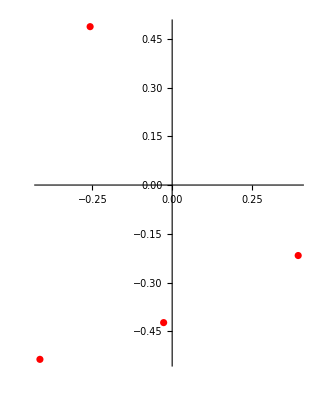
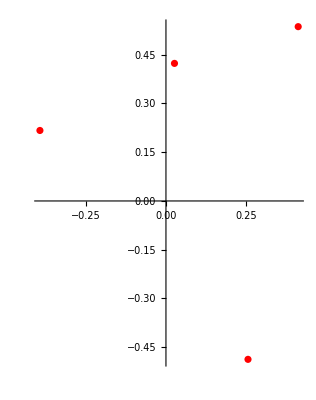
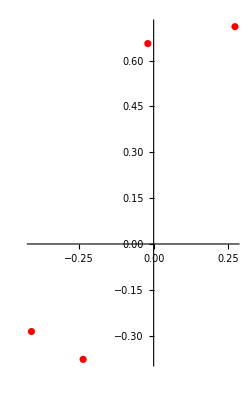
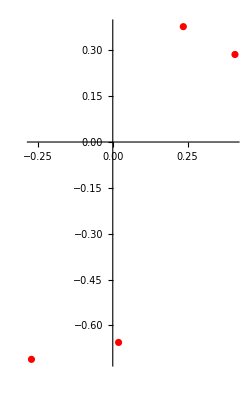
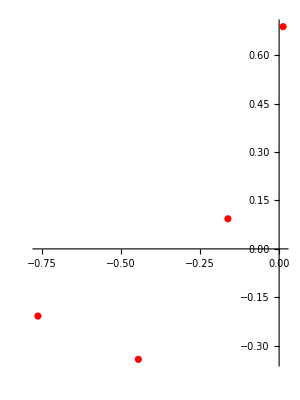
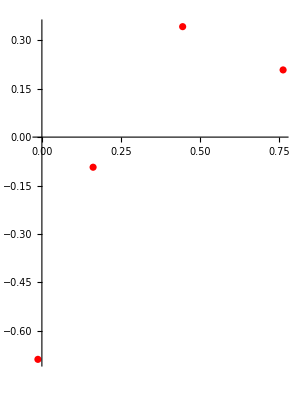
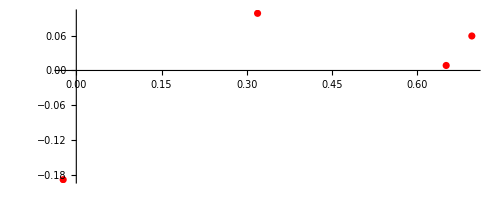
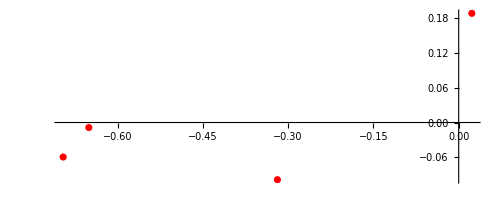

```mathematica
Table[ComplexListPlot[s[[i]],PlotStyle->Red],{i,8}]
```

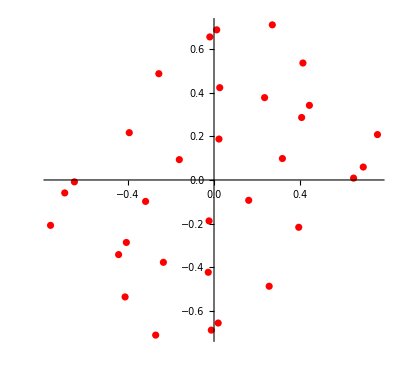

```mathematica
Show[%,PlotRange->All]
```

```mathematica
Table[Sum[s[[i,j]],{j,4}],{i,8}]
```

{-0.303261-0.689132 ⅈ,0.303261+0.689132 ⅈ,-0.391925+0.703084 ⅈ,0.391925-0.703084 ⅈ,-1.35532+0.231453 ⅈ,1.35532-0.231453 ⅈ,1.64167-0.0215453 ⅈ,-1.64167+0.0215453 ⅈ}

```mathematica
Abs[%]
```

{0.752908,0.752908,0.804943,0.804943,1.37494,1.37494,1.64181,1.64181}

```mathematica
Abs[%]*Sqrt[2]
```

{1.06477,1.06477,1.13836,1.13836,1.94445,1.94445,2.32187,2.32187}

```mathematica
Table[Sum[s[[i,j]]^2,{j,3}]-s[[i,4]]^2,{i,8}]//Chop
```

{-0.12501-0.843649 ⅈ,-0.12501-0.843649 ⅈ,-0.00444634+0.824121 ⅈ,-0.00444634+0.824121 ⅈ,-0.912658-0.0257143 ⅈ,-0.912658-0.0257143 ⅈ,0.776605+0.0397391 ⅈ,0.776605+0.0397391 ⅈ}

```mathematica
Apply[Plus,{-0.12501011559782219-0.8436485246051968 ⅈ,-0.12501011559783048-0.8436485246051968 ⅈ,-0.0044463370064570795+0.824120943503761 ⅈ,-0.004446337006441259+0.8241209435037838 ⅈ,-0.912657696000345-0.0257143406771837 ⅈ,-0.9126576960003427-0.02571434067718248 ⅈ,0.776605182127947+0.03973914527131581 ⅈ,0.7766051821279513+0.039739145271318374 ⅈ}]
```

-0.531018-0.0110056 ⅈ

```mathematica
s1=Join[s,{{-0.17164726199225983+0.3432945239845196 ⅈ,-0.3432945239845196-0.17164726199225983 ⅈ,0.06865890479690392-0.37762397638297157 ⅈ,0.7552479527659431-0.03432945239845192 ⅈ},{0.17164726199225983-0.3432945239845197 ⅈ,0.3432945239845197+0.17164726199225983 ⅈ,-0.06865890479690388+0.3776239763829716 ⅈ,-0.7552479527659434+0.034329452398451976 ⅈ}}]
```

{{-0.257071+0.487324 ⅈ,0.394874-0.216867 ⅈ,-0.0267151-0.423278 ⅈ,-0.414349-0.536312 ⅈ},{0.257071-0.487324 ⅈ,-0.394874+0.216867 ⅈ,0.0267151+0.423278 ⅈ,0.414349+0.536312 ⅈ},{-0.235789-0.37755 ⅈ,-0.408415-0.286493 ⅈ,0.271735+0.711244 ⅈ,-0.0194558+0.655884 ⅈ},{0.235789+0.37755 ⅈ,0.408415+0.286493 ⅈ,-0.271735-0.711244 ⅈ,0.0194558-0.655884 ⅈ},{-0.161709+0.0932893 ⅈ,0.0125752+0.688429 ⅈ,-0.444503-0.342151 ⅈ,-0.761679-0.208114 ⅈ},{0.161709-0.0932893 ⅈ,-0.0125752-0.688429 ⅈ,0.444503+0.342151 ⅈ,0.761679+0.208114 ⅈ},{0.650447+0.00860786 ⅈ,-0.0230976-0.187718 ⅈ,0.695546+0.0593131 ⅈ,0.318775+0.0982518 ⅈ},{-0.650447-0.00860786 ⅈ,0.0230976+0.187718 ⅈ,-0.695546-0.0593131 ⅈ,-0.318775-0.0982518 ⅈ},{-0.171647+0.343295 ⅈ,-0.343295-0.171647 ⅈ,0.0686589-0.377624 ⅈ,0.755248-0.0343295 ⅈ},{0.171647-0.343295 ⅈ,0.343295+0.171647 ⅈ,-0.0686589+0.377624 ⅈ,-0.755248+0.0343295 ⅈ}}

```mathematica
Length[s1]
```

10

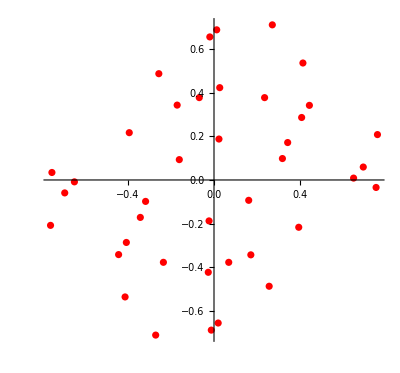

```mathematica
Show[Table[ComplexListPlot[s1[[i]],PlotStyle->Red,PlotRange->All],{i,10}],PlotRange->All]
```

```mathematica
(* solutions as Killing vectors in a Cartan matrix*)
```

```mathematica
ca=Table[2*s[[i]].s[[j]]/(s[[i]].s[[i]]),{i,8},{j,8}]//Chop
```

{{2.,-2.,-4.02772+1.94265 ⅈ,4.02772-1.94265 ⅈ,-0.62116-4.88872 ⅈ,0.62116+4.88872 ⅈ,1.4389+1.65065 ⅈ,-1.4389-1.65065 ⅈ},{-2.,2.,4.02772-1.94265 ⅈ,-4.02772+1.94265 ⅈ,0.62116+4.88872 ⅈ,-0.62116-4.88872 ⅈ,-1.4389-1.65065 ⅈ,1.4389+1.65065 ⅈ},{-1.37103-0.213411 ⅈ,1.37103+0.213411 ⅈ,2.,-2.,-2.01649+0.858522 ⅈ,2.01649-0.858522 ⅈ,0.788901-0.575715 ⅈ,-0.788901+0.575715 ⅈ},{1.37103+0.213411 ⅈ,-1.37103-0.213411 ⅈ,-2.,2.,2.01649-0.858522 ⅈ,-2.01649+0.858522 ⅈ,-0.788901+0.575715 ⅈ,0.788901-0.575715 ⅈ},{2.81718+0.0178067 ⅈ,-2.81718-0.0178067 ⅈ,-3.09567-2.59251 ⅈ,3.09567+2.59251 ⅈ,2.,-2.,-1.51695+1.20373 ⅈ,1.51695-1.20373 ⅈ},{-2.81718-0.0178067 ⅈ,2.81718+0.0178067 ⅈ,3.09567+2.59251 ⅈ,-3.09567-2.59251 ⅈ,-2.,2.,1.51695-1.20373 ⅈ,-1.51695+1.20373 ⅈ},{-0.685859-0.427735 ⅈ,0.685859+0.427735 ⅈ,-0.0468626+1.16088 ⅈ,0.0468626-1.16088 ⅈ,-1.11419-0.567532 ⅈ,1.11419+0.567532 ⅈ,2.,-2.},{0.685859+0.427735 ⅈ,-0.685859-0.427735 ⅈ,0.0468626-1.16088 ⅈ,-0.0468626+1.16088 ⅈ,1.11419+0.567532 ⅈ,-1.11419-0.567532 ⅈ,-2.,2.}}

```mathematica
Grid[ca]
```

2. | -2. | -4.02772+1.94265 ⅈ | 4.02772-1.94265 ⅈ | -0.62116-4.88872 ⅈ | 0.62116+4.88872 ⅈ | 1.4389+1.65065 ⅈ | -1.4389-1.65065 ⅈ
-2. | 2. | 4.02772-1.94265 ⅈ | -4.02772+1.94265 ⅈ | 0.62116+4.88872 ⅈ | -0.62116-4.88872 ⅈ | -1.4389-1.65065 ⅈ | 1.4389+1.65065 ⅈ
-1.37103-0.213411 ⅈ | 1.37103+0.213411 ⅈ | 2. | -2. | -2.01649+0.858522 ⅈ | 2.01649-0.858522 ⅈ | 0.788901-0.575715 ⅈ | -0.788901+0.575715 ⅈ
1.37103+0.213411 ⅈ | -1.37103-0.213411 ⅈ | -2. | 2. | 2.01649-0.858522 ⅈ | -2.01649+0.858522 ⅈ | -0.788901+0.575715 ⅈ | 0.788901-0.575715 ⅈ
2.81718+0.0178067 ⅈ | -2.81718-0.0178067 ⅈ | -3.09567-2.59251 ⅈ | 3.09567+2.59251 ⅈ | 2. | -2. | -1.51695+1.20373 ⅈ | 1.51695-1.20373 ⅈ
-2.81718-0.0178067 ⅈ | 2.81718+0.0178067 ⅈ | 3.09567+2.59251 ⅈ | -3.09567-2.59251 ⅈ | -2. | 2. | 1.51695-1.20373 ⅈ | -1.51695+1.20373 ⅈ
-0.685859-0.427735 ⅈ | 0.685859+0.427735 ⅈ | -0.0468626+1.16088 ⅈ | 0.0468626-1.16088 ⅈ | -1.11419-0.567532 ⅈ | 1.11419+0.567532 ⅈ | 2. | -2.
0.685859+0.427735 ⅈ | -0.685859-0.427735 ⅈ | 0.0468626-1.16088 ⅈ | -0.0468626+1.16088 ⅈ | 1.11419+0.567532 ⅈ | -1.11419-0.567532 ⅈ | -2. | 2.

```mathematica
Eigenvalues[ca]//Chop
```

{15.134-3.75085 ⅈ,-0.391575+5.49899 ⅈ,2.229+0.00352565 ⅈ,-0.971397-1.75167 ⅈ,0,0,0,0}

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
(*end*)
```